```mathematica
Q= 2. π{-1/2, -1/2, 1/2};
q=2. π{1/2,1/2,1/2};

kinS[th_,ph_]:=2π(0.792){Sin[th]Cos[ph],Sin[th]Sin[ph],Cos[th]}

kin=2 π{0., 0.792, 0.041};
kA2=2 π{-0.5,0.292,0.541};


sk[Lc_,th_,ph_]:=
Module[{kin,Q,sumlim},
sumlim=16;
kin=kinS[th,ph];
Q=kA2-kin;
Chop[Sum[Exp[I (Q+q).{ri, rj, rk}]Exp[-√(ri^2+rj^2+rk^2)/Lc],{ri,-sumlim,sumlim},{rj,-sumlim,sumlim},{rk,-sumlim,sumlim}]]
]
```

```mathematica
theta=0.483 π;
phi=0.500 π;

l5=Table[{dph,sk[5.,theta,phi+dph]/2500.},{dph,-0.2,0.2,0.0125}];
l10=Table[{dph,sk[10.,theta,phi+dph]/8000.},{dph,-0.2,0.2,0.0125}];
l15=Table[{dph,sk[15.,theta,phi+dph]/13000.},{dph,-0.2,0.2,0.0125}];
l3=Table[{dph,sk[3.,theta,phi+dph]/640.},{dph,-0.2,0.2,0.0125}];
```

```mathematica
l1p5=Table[{dph,sk[1.5,theta,phi+dph]/90.},{dph,-0.2,0.2,0.0125}];
```

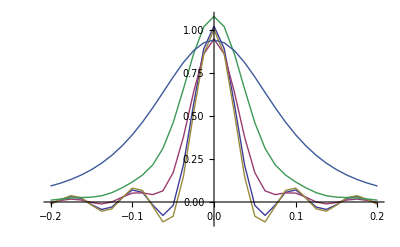

```mathematica
ListPlot[{l10,l5,l15,l3,l1p5},PlotRange->All,Joined->True]
```

```mathematica
f=(Γ/2)/(Δ+I Γ/2);
fc=(Γ/2)/(Δ-I Γ/2);
FullSimplify[f fc]
```

Γ^2/(Γ^2+4 Δ^2)